```mathematica
Clear["Global`*"]
```

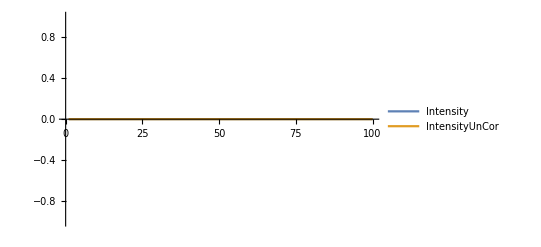

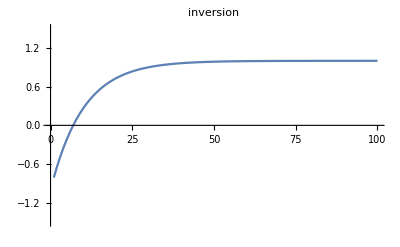

-Graphics-

```mathematica
(*When doing one run*)
name ="test";
intensity=Flatten[Import[NotebookDirectory[]<>name<>"/intensity.dat"]];
intensityUnCor=Flatten[Import[NotebookDirectory[]<>name<>"/intensityUnCor.dat"]];
inversion=Flatten[Import[NotebookDirectory[]<>name<>"/inversion.dat"]];
spinSpinCor=Flatten[Import[NotebookDirectory[]<>name<>"/spinSpinCor.dat"]];
ListLinePlot[{intensity,intensityUnCor},PlotRange->All,PlotLegends->{"Intensity","IntensityUnCor"}]
ListLinePlot[inversion,PlotLabel->"inversion",PlotRange->{-1,1}]
ListLinePlot[spinSpinCor,PlotRange->All,PlotLabel->"spinSpinCor"]
```